## Глава 3 Операционное исчисление в СКМ Mathematica

## §3.1. Преобразование Лапласа

### 3.1.1. Определение и свойства преобразования Лапласа.

Преобразованием Лапласа функции f(t), t∈ℝ (которая, может принимать и комплексные значения), называется функция F(p) комплексной переменной p, пределяемая следующим равенством:

F(p)=∫_0^(+∞) e^(-p t)f(t)ⅆt

Оригиналом называется всякая функция f(t), удовлетворяющая следующим условиям:

1) f(t)=0 при t<0, причем принимается, что f(0)=f(+0);

2) Существуют такие постоянные σ и M, что:

|f(t)|<M ⅇ^(σ t) при t>0

(величина σ_0=inf σ называется показателем роста функции f(t));

3) На любом конечном отрезке [0;T] функция может иметь лишь конечное число точек разрыва, причем только 1-ого рода.

Если f(t) - оригинал, то стоящий в правой части равенства (1) интеграл Лапласа сходится абсолютно и равномерно в полуплоскости Re p  ⩾ σ>σ_0. При этом функция F(p) является аналитической в полуплоскости Re p> σ_0 и называется изображением функции f(t).

Соответствие между оригиналом f(t) и его изображением F(p) символически записывается в виде f(t)≐F(p)

##### Пример №13.10

Рассмотрим простейший пример: Используя формулу (1.1.1), найти изображение для следующего оригинала:

f(t)=Piecewise[{{t, 0≤ t<2}, {1/2(4-t), 2≤ t<4}, {0, 4≤ t}}]

Запишем заданную кусочно-заданную функцию:

```mathematica
f[t_]:=Piecewise[{{t,0≤ t<2},{1/2(4-t),2≤ t<4}},0]
```

Для наглядности построим график функции:

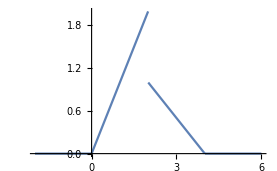

```mathematica
Plot[f[t],{t,-2,6}]
```

Очевидно, что данная функция является оригиналом, т.к. соблюдены все условия изложенные выше.

Для того чтобы найти изображение, воспользуемся формулой (1). Обозначать изображения будем fp(p) т.к. функции начинающиеся с большой буквы в основном являются системными т.е. встроенными.

```mathematica
fp[p_]:=Integrate[Exp[-p t]f[t],{t,0,Infinity}]
```

```mathematica
fp[p_]:=Integrate[Exp[-k t]f[t],{t,0,Infinity}]/.k-> p
```

Существует принципиальное отличие, между двемя выражениями, записанными выше. Первое интерпретируется следующим образом: каждый раз при вызове функции fp(p_1) в переменную p, стоящую внутри интеграла, передается значение p_1 и затем вычисляется весь интеграл. Можно догадаться, что это замедляет работу программы, поэтому используется второй способ: сначала вычисляется интеграл, зависящий от k, затем переменная k просто заменяется на значение p_1. Данный способ работает быстрее, т.к. интеграл не будет вычисляться столько раз, сколько раз мы вызвали функцию fp(p) .

Выведем полученную функцию:

```mathematica
fp[p]
```

(ⅇ^(-4 p) (1-3 ⅇ^(2 p)+2 ⅇ^(4 p)-2 ⅇ^(2 p) p))/(2 p^2)

Ответ:

f(t)≐(ⅇ^(-4 p) (1-3 ⅇ^(2 p)+2 ⅇ^(4 p)-2 ⅇ^(2 p) p))/(2 p^2)

##### Пример №1

Найти изображение функции Хевисайда:

H(t)=η(t)=Piecewise[{{1, t≥ 0}, {0, t<0}}]

Функция Хевисайда в Mathematica является встроенной функцией, конечно можно определить ее самостоятельно при помощи кусочно-заданной функции PieceWise, но в этом нет необходимости. Записывается следующим образом:

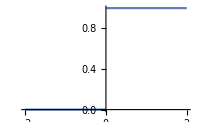

```mathematica
h[t_]:=HeavisideTheta[t]
Plot[h[t],{t,-2,2}]
```

Так как функция Хевисайда является оригиналом, то ее изображение:

```mathematica
hp[p_]:=Integrate[Exp[-k t]h[t],{t,0,Infinity}]/.k-> p
```

```mathematica
Simplify[hp[p],Re[p]>0]
```

1/p

Получили H(t)≐p^-1.

### 3.1.2 Свойства преобразования Лапласа.

1. С в о й с т в о  л и н е й н о с т и.

∑_(k=1)^n C_k f_k(t)≐∑_(k=1)^n C_k F_k(p),  Re p> max{σ_1,σ_2,... σ_n}

2. Т е о р е м а  п о д о б и я.

f(t/α)≐1/α F(p/α), Re p>α σ_0

3. Т е о р е м а  с м е щ е н и я. Умножению оригинала на ⅇ^(α t),α∈ℝ, соответствует смещение аргумента изображения на α, т.е.:

ⅇ^(α t)f(t)≐F(p-α), Re(p-α)>σ_0

4. Т е о р е м а   з а п а з д ы в а н и я. Запаздыванию оригинала на τ соответсвует умножение изображения на ⅇ^(-p τ):

η(t-τ)f(t)≐ⅇ^(-p τ)F(p), Re p > σ_0

5. Д и ф ф е р е н ц и р о в а н и е  о р и г и н а л а.  Если f(t) и ее производные f^(k)(t) являются оригиналами, то для любого k=1,2...n

f^(k)(t)≐p^k F(p)-(p^(k-1)f(0)+p^(k-2)f'(0)+...+f^(k-1)(0))

В частности,

f'(t)≐p F(p)-f(0), Re p> σ_0

6. И н т е г р и р о в а н и е  о р и г и н а л а:

∫_0^t f(τ)ⅆτ≐(F(p))/p, Re p> σ_0

7. Д и ф ф е р е н ц и р о в а н и е  и з о б р а ж е н и я. Умножению оригинала на множитель t соответствует умножению изображения на -1 и дифференцирование его по аргументу  p:

(t
□)^n f(t)≐(-1)^n F^(n)(p), n=1,2...

8. И н те г р и р о в а н и е  и з о б р а ж е н и я. Если f(t)/t является оригиналом, то

1/t f(t)≐∫_p^(+∞) F(q)ⅆq

9. Д и ф ф е р е н ц и р о в а н и е  и  и н т е г р и р о в а н и е  п о  п а р а м е т р у. Если f(t,α)≐F(p,α) и функции ∂/(∂α)f(t,α) и ∫_α1^α2 f(t,α)ⅆα, рассматриваемые как функции переменной t, являются оригиналами, то

∂/(∂α)f(t,α)≐∂/(∂α)F(p,α)      и      ∫_α1^α2 f(t,α)ⅆα=∫_α1^α2 F(p,α)ⅆα

10. Т е о р е м а  Б о р е л я  о б  и з о б р а ж е н и и  с в е р т к и. Свертке оригиналов

f_1*f_2=∫_0^t f_1(τ)f_2(t-τ)ⅆτ=∫_0^t f_1(t-τ)f_2(τ)ⅆτ

соответствует произведение изображений, т. е.

f_1*f_2=F_1(p)·F_2(p)

11. И н т е г р а л  Д ю а м е л я. Если f(t)≐F(p) и g(t)≐G(p), то

p F(p) G(p)≐f(o)g(t)+(f'*g)(t)=g(0)f(t)+(g'*f)(t)

Ниже приведен список изображений наиболее распространенных функций:

η(t)≐1/p                                                      t^n≐(n!)/p^(n+1)
ch β t≐p/(p^2-β^2)                          sh β t≐β/(p^2-β^2)
ⅇ^(α t)≐1/(p-α)                           t^n ⅇ^(α t)≐(n!)/(p-α)^(n+1)
cos β t ≐p/(p^2+β^2)                      sin β t≐β/(p^2+β^2)

С помощью свойств преобразования Лапласса и списка основных изображений можно найти изображения большинства функций встречающихся на практике.

Рассмотрим пример:

##### Пример №13.19

Найти изображение заданной функции:

f(t)=e^-t+3 e^(-2t)+t^2

Согласно свойству линейности, изображение суммы функций равно сумме изображений, и используя список изображений, имеем:

e^-t=1/(p+1)
3 e^(-2t)=3/(p+2)
t^2=2/p^3

В итоге, изображение исходной функции:

f(t)≐F(p)
F(p)=1/(p+1)+3/(p+2)+2/p^3

##### Пример №13.22

Найти изображение заданной функции:

f(t)=sin^2(t-a)

Применяя тригонометрические тождества, приведем функцию к виду:

sin^2(t-a)=1/2(1-cos(2(t-a)))
cos(2(t-a))=cos 2t cos 2a + sin 2t sin 2a
sin^2(t-a)=1/2(1-cos 2t cos 2a - sin 2t sin 2a)

Воспользуемся свойством линейности и списком изображений:

cos 2t≐p/(p^2+4),  sin 2t≐2/(p^2+4)

Получаем изображение исходной функции:

F(p)=1/2(1/p-(p cos 2a)/(p^2+4)-(2sin 2a)/(p^2+4))

##### Пример №13.32

Найти изображение заданной функции:

f(t)=ⅇ^-t sin^2(t)

Чтобы найти изображение, воспользуемся выражением полученным в предыдущем примере. Так как a=0, то:

(sin(t))^2≐1/2(1/p-p/(p^2+4))

Теперь, согласно теореме смещения, получаем ответ:

ⅇ^-t sin^2(t)≐1/2(1/(p+1)-p/((p+1)^2+4))

##### Пример №13.36

Найти изображение заданной функции:

f(t)=∫_0^t ⅇ^(-1/2(t-τ))τⅆτ

Заданная функция представляет из себя свертку двух функций:

ⅇ^(-1/2t)*t=∫_0^t ⅇ^(-1/2(t-τ))τⅆτ=∫_0^t ⅇ^(-1/2τ)(t-τ)ⅆτ

По теореме Бореля об изображении свертки, получаем изображение:

ⅇ^(-1/2t)*t≐1/p^2 1/(p+1/2)=2/(p^2(2p+1))

##### Пример №13.44

Найти изображение дифференциального выражения при заданных начальных условиях:

x^IV(t)+4x'''(t)+2x''(t)-3x'(t)-5,  x(0)=x'(0)=x''(0)=x'''(0)=0

Обозначит изображение функции x(t) как X(p), тогда согласно свойству дифференцирования оригинала получаем:

x^IV(t)≐p^4 X(p)-(p^3 f(0)+p^2 f'(0)+p f''(0)+f'''(0)=p^4 X(p)

Так как начальные условия нулевые, получим следующее изображение исходного выражения:

X(p)(p^4+4 p^3+2 p^2-3p)-5/p

Все рассмотренные выше примеры мало относятся к теме данной книги - компьютерной технологии. Они были решены традиционными методами, в каждой задаче приходилось выбирать нужные свойства и каждый раз смотреть в таблицу изображений. Разумеется процесс решения данного класса задач может быть существенно упрощен с использованием внутренних функций Mathematica. Рассмотрим простейший пример.

##### Пример №13.27

Найти изображение заданной функции:

f(t)=sin t- t cos t

В обычном случае, нам необходимо было бы воспользоваться рядом свойств (линейности и дифференцирование изображения), чтобы с помощью изображений известных простейших функций получить изображение заданной.

Функция LaplaceTransform заменяет все эти действия. Рассмотрим прмер работы:

```mathematica
LaplaceTransform[Cos[t],t,p]
```

p/(1+p^2)

```mathematica
LaplaceTransform[t Cos[t],t,p]
```

(-1+p^2)/((1+p^2)^2)

Данная функция сама подбирает нужные свойства и находит изображение.

Изображение заданной функции:

```mathematica
LaplaceTransform[Sin[t]-Cos[t]t,t,p]
```

-(-1+p^2)/((1+p^2)^2)+1/(1+p^2)

Рассмотрим ряд примеров:

##### Пример №13.25

f(t)=sh (3t) cos (2t)

```mathematica
LaplaceTransform[Sinh[3t]Cos[2t],t,p]
```

-(3 (13-p^2))/((13-6 p+p^2) (13+6 p+p^2))

F(p)=-(3 (13-p^2))/((13-6 p+p^2) (13+6 p+p^2))

##### Пример №13.37

f(t)=∫_0^t (t-τ)^2 cos 2τⅆτ

```mathematica
LaplaceTransform[Integrate[(t-τ)^2 Cos[2τ],{τ,0,t}],t,p]//Simplify
```

2/(4 p^2+p^4)

F(p)=2/(4 p^2+p^4)

##### Пример №13.42

f(t)=∫_0^t (cos β τ-cos α τ)/τ ⅆτ

```mathematica
LaplaceTransform[Integrate[(Cos[β τ]-Cos[α τ])/τ,{τ,0,t}],t,p]
```

Log[1+p^2/α^2]/(2 p)+Log[α]/p-Log[1+p^2/β^2]/(2 p)-Log[β]/p

F(p)=1/(2p)ln((α^2+p^2)/(β^2+p^2))

Также, с помощью данной функции, становится удобно находить изображения дифференциальных выражений:

##### Пример №13.42

Найти изображение дифференциального выражения при заданных начальных условиях:

x'''(t)+6x''(t)+x'(t)-2x(t),     x(0)=x'(0)=0,   x''(0)=1

Воспользуемся функцией LaplaceTransofrm непосредственно на всё выражение:

```mathematica
LaplaceTransform[x'''[t]+6x''[t]+x'[t]-2x[t],t,p]
```

-2 LaplaceTransform[x[t],t,p]+p LaplaceTransform[x[t],t,p]+p^3 LaplaceTransform[x[t],t,p]-x[0]-p^2 x[0]+6 (p^2 LaplaceTransform[x[t],t,p]-p x[0]-x'[0])-p x'[0]-x''[0]

Обратим внимание на LaplaceTransorm[x[t],t,p]. Данная функция, зависящая от p, есть ни что иное, как изображение функции x(t). Заменим его на X(p):

```mathematica
LaplaceTransform[x'''[t]+6x''[t]+x'[t]-2x[t],t,p]/.LaplaceTransform[x[t],t,p]-> X[p]
```

-x[0]-p^2 x[0]-2 X[p]+p X[p]+p^3 X[p]+6 (-p x[0]+p^2 X[p]-x'[0])-p x'[0]-x''[0]

Теперь, таким же образом, можно учесть начальные условия:

```mathematica
LaplaceTransform[x'''[t]+6x''[t]+x'[t]-2x[t],t,p]/.{LaplaceTransform[x[t],t,p]-> X[p],x[0]-> 0,x'[0]-> 0,x''[0]-> 1}
```

-1-2 X[p]+p X[p]+6 p^2 X[p]+p^3 X[p]

В итоге получили:

-1+X(p)(-2 +p+6 p^2+p^3 )

##### Модуль

Составим мини программный модуль, который будет находить изображения дифференциальных выражений с учетом начальных условий (или без них):

```mathematica
laplaceD[t_,expr_,rule_]:=Module[{},
Collect[LaplaceTransform[expr,t,p]/.LaplaceTransform[x[t],t,p]-> X[p]/.rule,X[p]]]
```

Пример работы:

##### Пример №13.46

Найти изображение дифференциального выражения при заданных начальных условиях:

x''(t)+5x'(t)-7x(t)+2,     x(0)=α, x'(0)=0

```mathematica
laplaceD[t,x''[t]+5x'[t]-7x[t]+2,{x[0]-> α,x'[0]-> 0}]
```

2/p-5 α-p α+(-7+5 p+p^2) X[p]

##### Пример №13.113

Найти изображение дифференциального выражения при заданных начальных условиях:

x''(t)-2x'(t)+2x=sin t, x(0)=0,  x'(0)=1

```mathematica
laplaceD[t,x''[t]-2x'[t]+2x[t]-Sin[t],{x[0]-> 0,x'[0]-> 1}]
```

-1-1/(1+p^2)+(2-2 p+p^2) X[p]

##### Пример №13.53

Найти изображение следующей функции:

f(t)=Piecewise[{{h/τ t, 0≤ t<τ}, {h, τ≤t≤ 2τ}, {-h/τ(t-3τ), 2τ≤ t<3τ}, {0, t≥ 3τ}}]

Данный пример не представляет абсолютно никакой сложности, решим его при помощи функции LaplaceTransform.

Запишем функцию:

```mathematica
f[t_]:=Piecewise[{{h/τ t,0≤ t<τ},{h,τ≤ t< 2τ},{-h/τ(t-3τ),2τ≤ t<3τ}}]
```

Построим ее график, при h=1,τ=π:

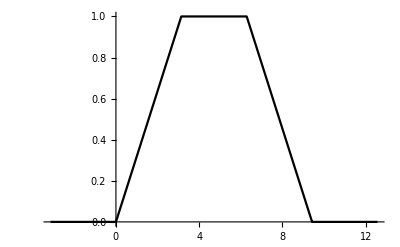

```mathematica
Plot[f[t]/.{h-> 1,τ-> Pi},{t,-1Pi,4Pi}]
```

Теперь найдем изображение:

```mathematica
Simplify[LaplaceTransform[f[t],t,p],τ>0]
```

(ⅇ^(-3 p τ) (-1+ⅇ^(p τ))^2 (1+ⅇ^(p τ)) h)/(p^2 τ)

На этом этапе, оставим тему поиска изображений.

## §3.2. Восстановление оригинала по изображению

### 3.2.1. Формула обращения. Теоремы разложения.

Если f(t)- оригинал и F(p)- его изображение, то в любой точке непрерывности f(t) справедлива формула обращения Меллина

f(t)=1/(2π ⅈ)∫_(σ-ⅈ ∞)^(σ+ⅈ ∞) F(p)ⅇ^(p t)ⅆp

где интегрирование производится по любой прямой Re p=σ, σ>σ_0.

Непосредственное применение формулы обращения чсто затруднительно, и обычно пользуются теоремами разложения, являющимися следствиями из нее:

П е р в а я  т е о р е м а  р а з л о ж е н и я. Если функция F(p) аналитична в некоторой окрестности бесконечно удаленной точки и ее разложение в ряд по степеням 1/p имеет вид

F(p)=∑_(n=0)^∞ a_n/p^(n+1),

то функция

f(t)=∑_(n=0)^∞ a_n t^n/(n!), t≥ 0 (f(t)=0 при t<0)

является оригиналом, имеющим изображение F(p).

В т о р а я  т е о р е м а  р а з л о ж е н и я. Если изображение F(p) является однозначной функцией и имеет лишь конечное число особых точек p_1,p_2,... p_n, лежащих в конечной части полуплоскости Re p⩽σ_0, то

f(t)=∑_(k=1)^n res[e^(p t)F(p); p_k]

Если в частности, F(p)=P_m(p)/Q_n(p), где P_m(p) и Q_n(p) - многочлены степеней m и n соответственно (n>m), p_1,p_2,... p_r - корни многочлена Q_n(p) с кратностями, соответственно равными  j_1, j_2, ... j_r, то

f(t)=∑_(k=1)^r 1/((j_k-1)!)lim_(p→p_k) ⅆ^(j_k-1)/(ⅆ p^(j_k-1))((p-p_k)^j_k F(p) e^(p t))

Примечание. Если все корни p_i - простые (j_i=1), то формула (2) упрощается до вида:

f(t)=∑_(k=1)^n (P_m(p_k))/(Q_n'(p_k))e^(p_k t)

##### Пример 13.88

Пользуясь первой теоремой разложениия, найти оригинал для заданной функции

F(p)=1/p cos(1/p)

Согласно первой теореме, находим разложение в ряд F(p) в окрестности бесконечно удаленной точки. 
Вычислим n-ый коэффициент этого разложения:

```mathematica
Series[1/p Cos[1/p],{p,Infinity,7}]
```

1/p-1/(2 p^3)+1/(24 p^5)-1/(720 p^7)+O[1/p]^8

```mathematica
c[n_]:=SeriesCoefficient[1/p Cos[1/p],{p,Infinity,n}]
```

```mathematica
Refine[c[n],n>1]
```

(ⅈ ⅈ^n (-1+(-1)^n))/(2 (-1+n)!)

Итак, получили разложение изображения F(p) в ряд:

1/p cos(1/p)=∑_(n=1)^∞ c_n 1/p^n=∑_(n=0)^∞ c_(n+1)1/p^(n+1)

По первой теореме находим оригинал данного изображения изображения:

f(t)=∑_(n=0)^∞ c_(n+1)t^n/(n!)

Запишем выражение функции оригинала:

```mathematica
f[t_,k_]:=Sum[c[n+1]/n! t^n,{n,0,k}]
```

```mathematica
f[t,10]
```

1-t^2/4+t^4/576-t^6/518400+t^8/1625702400-t^10/13168189440000

Преобразуем выражение для коэффициента:

```mathematica
Refine[c[n+1]/n!,n>0]
```

(ⅈ ⅈ^(1+n) (-1+(-1)^(1+n)))/(2 (n!)^2)

(ⅈ ⅈ^(1+n) (-1+(-1)^(1+n)))/(2 (n!)^2)=Piecewise[{{(-2(i)^(2+n))/(2(n!)^2), n=2m}, {0, n=2m+1}}]

В итоге функция-оригал имеет вид:

f(t)=∑_(m=0)^∞ (-1)^m t^(2m)/((2m)!)^2

Разумеется каждый раз проделывать такую утомительную последовательность действий не рационально. Составим программный обучающий модуль, который будет выдавать нам ответ в традиционной форме.

##### Программный модуль (обучающая программа).

Проанализируем основную последовательность необходимых действий на основе примера №13.89:

F(p)=sin(1/p)

Сначала находим выражение для n+1 коэффициента:

```mathematica
c[n_]:=SeriesCoefficient[Sin[1/p],{p,Infinity,n+1}]
```

```mathematica
c[n]
```

Piecewise[{{(ⅈ ⅈ^(1+n) (-1+(-1)^(1+n)))/(2 (1+n)!), 1+n≥0}, {0, True}}]

Затем уходим от кусочно-заданной функции при помощи функции Refine:

```mathematica
Refine[c[n],n>1]
```

(ⅈ ⅈ^(1+n) (-1+(-1)^(1+n)))/(2 (1+n)!)

Мы можем также преобразовать выражение для коэффициента с учетом того, что n - четное число:

```mathematica
Refine[c[n],n>1&&Mod[n,2]==0]//Simplify
```

ⅈ^n/((1+n)!)

Но к сожалению, способ делать это автоматически сложен и в нем нет необходимости.

Теперь необходимо домножить коэффициент на t^n/n!, и просуммировать от 0 до бесконечности. Но так как на выходе мы хотим получить лишь запись в традиционной форме, воспользуемся функцией Inactivate, которая как следует из названия дезактивирует функцию, следующую за ней:

```mathematica
Inactivate[ Sum[x^n,{n,1,45}],Sum]
```

x^nn145

И затем просто добавим опцию TraditionalForm для формульного отображения:

```mathematica
TraditionalForm@Inactivate[Sum[Refine[c[n],n>1] t^n/n!,{n,0,Infinity}],Sum]
```

(ⅈ ⅈ^(n+1) ((-1)^(n+1)-1) t^n)/(2 n! (n+1)!)n0∞

Итак, после того как мы изучили основные шаги, соберем это всё как и прежде в единый модуль:

##### Программный модуль

```mathematica
findOriginalS[p_,F_,t_]:=Module[{},TraditionalForm@Inactivate[Sum[Refine[SeriesCoefficient[F,{p,Infinity,n+1}]*t^n/(n)!,n≥ 8],{n,0,Infinity}],Sum]]
```

Зачем это нужно? Конечно раз мы не объявляем никаких локальных переменных, то модуль здесь просто не нужен. Его применение объясняется лишь стилистикой данной книги.

Продемонстрируем пример:

```mathematica
findOriginalS[p,1/p Exp[1/p],t]
```

t^n/(n!)^2n0∞

```mathematica
findOriginalS[p,1/(2p)Log[(p+1)/(p-1)],t]
```

(((-1)^(n+1)+1) t^n)/(2 n n!)n0∞

Также можем составить модуль, который будет считать сумму бесконечного сходящегося ряда:

```mathematica
findOriginal[p_,F_,t_]:=Module[{},TraditionalForm@Sum[Refine[SeriesCoefficient[F,{p,Infinity,n+1}]*t^n/(n)!,n≥ 8],{n,0,Infinity}]]
```

```mathematica
findOriginal[p,1/(2p)Log[(p+1)/(p-1)],t]//FullSimplify
```

t-(ⅈ π)/2

```mathematica
findOriginal[p,1/p Exp[1/p],t]
```

02 √t

Вдаваться в подробности полученных специальных функций мы не будем. Информацию о них можно получить в учебниках по математическому анализу, либо же в разделе Help.

##### Пример №13.93

Пользуясь второй теоремой разложения, найти оригинал для заданной функции:

F(p)=p/(p^2+4p+5)

Согласно второй теореме разложения (1), оригнал функции найдем как сумму вычетов функции ⅇ^(p t) F(p).

Для этого найдем полюса исходной функции F(p):

```mathematica
F[p_]:=p/(p^2+4p+5)
```

```mathematica
sol=p/.Solve[Denominator[F[p]]==0,p]
```

{-2-ⅈ,-2+ⅈ}

Теперь чтобы найти функцию-оригинал, просуммируем вычеты:

```mathematica
Sum[Residue[Exp[t p]F[p],{p,sol[[i]]}],{i,1,Length[sol]}]//FullSimplify
```

ⅇ^(-2 t) (Cos[t]-2 Sin[t])

Получили, что:

p/(p^2+4p+5)≐ⅇ^(-2t)(cos(t)-2sin(t))

##### Программный модуль

Анализируя несложную последовательность действий,на основе опыта предыдущей задачи, составим программный модуль:

```mathematica
findOriginalR[p_,F_,t_]:=Module[{sol},
sol=p/.Solve[Denominator[F]==0,p];
FullSimplify@Sum[Residue[Exp[p t]F,{p,sol[[i]]}],{i,1,Length[sol]}]]
```

Продемонстрируем пример работы:

##### Пример 13.94

```mathematica
findOriginalR[p,(p+2)/((p+1)(p-2)(p^2+4)),t]
```

1/30 (-3 Cos[2 t]-2 Cosh[t]+5 Cosh[2 t]-6 Sin[2 t]+2 Sinh[t]+5 Sinh[2 t])

##### Пример 13.99

```mathematica
findOriginalR[p,p^5/(p^6-1),t]
```

1/3 (2 Cos[(√3 t)/2] Cosh[t/2]+Cosh[t])

##### Пример 13.104

```mathematica
findOriginalR[p,p^3/((p^4-1)(p^4+4)),t]
```

1/10 (Cos[t]+Cosh[t]-2 Cos[t] Cosh[t])

##### Встроенные средства

Mathematica имеет встроенное обратное преобразование функции-изображения в функцию-оригинал. Опция InverseLaplaceTransofrm, которая имеет схожую структуру с опцией LaplaceTransform.

Рассмотрим примеры применения:

##### Пример 13.80

```mathematica
InverseLaplaceTransform[p/((p^2-4 )(p^2+1)),p,t]
```

ⅇ^(-2 t)/10+ⅇ^(2 t)/10-Cos[t]/5

##### Пример 13.86

```mathematica
InverseLaplaceTransform[1/(p-2)+Exp[-p]/p+3 Exp[-4p]/(p^2+9),p,t]
```

ⅇ^(2 t)+HeavisideTheta[-1+t]+HeavisideTheta[-4+t] Sin[3 (-4+t)]

##### Пример 13.89

```mathematica
InverseLaplaceTransform[1/p Exp[1/p^2],p,t]
```

InverseLaplaceTransform[(ⅇ^(1/p^2))/p,p,t]

##### Пример 13.100

```mathematica
InverseLaplaceTransform[p^3/((p^2+1)^3),p,t]
```

1/8 (t^2 Cos[t]+3 t Sin[t])

Как мы видим, функция InverseLaplaceTransofrm работает практически со всеми видами функций-изображений, имеет широкую область применений, но в сложных случаях (13.89) не дает результата. В дальнейшем, при необходимости найти оригинал изображения будем пользоваться ей, в случае если это приведет к положительному результату.

## 3.3. Применение операционного исчисления

### 3.3.1. Решение линейных дифференциальных уравнений и систем уравнений с постоянными коэффициентами.

Для того чтобы найти решение x(t) линейного дифференциального уравнения с постояными коэффициентами

x^(n)+a_1 x^(n-1)+...+a_n x=f(t)

(где f(t) - оригинал), удовлетворяющее начальным условиям

x(0)=x_0,x'(0)=(x')_0,...,x^(n-1)(0)=(x^(n-1))_0

следует применить к обеим частям этого уравнения преобразование Лапласа, т.е. от уравнения (1) с условиями (2) перейти к операторному уравнению

(p^n+a_1 p^(n-1)+...+a_n)X(p)+Q(p)=F(p),

где X(p)- изображение искомого решения, F(p)- изображение функции f(t), а Q(p) - некоторый многочлен, коэффициенты которого зависят от начальных данных (2) и который тождественно равен нулю, если x_0=(x')_0=...=(x^(n-1))_0=0. Решим операторное уравнение относительно X(p):

X(p)=(F(p)-Q(p))/(L(p))

L(p)=p^n+a_1 p^(n-1)+...+a_n- характеристический многочлен

и найдя оригинал для X(p), мы получим искомое решение x(t). Если считать x_0,(x')_0,...,(x^(n-1))_0 произвольными постоянными, то найденное решение будет общим решением уравнения (1). Совершенно аналогично решаются и системы линейных дифференциальных уравнений с постоянными коэффициентами. Отличие будет лишь в том, что вместо одного операторного уравнения мы получим систему таких уравнений, которые будут линейными относительно изображений искомых функций.

##### Пример №13.105

Найти общее решение дифференциального уравнения:

x''+9x=cos 3t

Найдем изображение этого уравнения, при помощи модуля laplaceD из параграфа 3.1.2:

```mathematica
dif=laplaceD[t,x''[t]+9x[t]-Cos[3t],{}]
```

-p/(9+p^2)-p x[0]+(9+p^2) X[p]-x'[0]

Получили изображение исходного уравнения, прировняем к 0 и выразим искомую функцию X(p):

```mathematica
Solve[dif==0,X[p]]
```

{{X[p]→(p+9 p x[0]+p^3 x[0]+9 x'[0]+p^2 x'[0])/((9+p^2)^2)}}

Получили выражение для изображения искомой функции, найдем саму функцию:

```mathematica
InverseLaplaceTransform[(p+9 p x[0]+p^3 x[0]+9 x'[0]+p^2 x'[0])/((9+p^2)^2),p,t]//TraditionalForm
```

1/6 (2 sin(3 t) x'(0)+6 x(0) cos(3 t)+t sin(3 t))

Итак получили решение дифференциального уравнения:

x(t)=1/6 (2 sin(3 t) x'(0)+6 x(0) cos(3 t)+t sin(3 t))

Обозначим начальные условия x(0)=C_1, x'(0)/3=C_2, тогда получим общее решение:

x(t)=С_1 cos(3 t)+С_2 sin(3 t) +1/6 t sin(3 t)

##### Пример №13.111

Найти решение дифференциального уравнения при заданных начальных условиях:

x''+2x'+x=ⅇ^-t,x(0)=1,x'(0)=0

Найдем изображение:

```mathematica
dif=laplaceD[t,x''[t]+2x'[t]+x[t]-Exp[-t],{x[0]-> 1,x'[0]-> 0}]
```

-2-p-1/(1+p)+(1+2 p+p^2) X[p]

Получим выражение для изображения:

```mathematica
Solve[dif==0,X[p]]
```

{{X[p]→(3+3 p+p^2)/(1+p)^3}}

Тогда найдем решение:

```mathematica
InverseLaplaceTransform[(3+3 p+p^2)/(1+p)^3,p,t]
```

1/2 ⅇ^-t (2+2 t+t^2)

Решение исходного дифференциального уравнения:

x(t)=1/2 ⅇ^-t (2+2 t+t^2)

##### Программный модуль

Составим простой программный модуль решения дифференциального уравнения:

```mathematica
dsolve[t_,expr_,rule_]:=Module[{im,xp},
im=LaplaceTransform[expr,t,p]/.LaplaceTransform[x[t],t,p]-> X[p]/.rule;
xp=X[p]/.Flatten@Solve[im,X[p]];
InverseLaplaceTransform[xp,p,t]//Simplify
]
```

##### Пример №13.117

Найти решение дифференциального уравнения:

x^IV-x=sh t, x(0)=x'(0)=x''(0)=0,   x'''(0)=1

Найдем решение при помощи созданного нами модуля:

```mathematica
dsolve[t,x''''[t]-x[t]==Sinh[t],{x[0]-> 0,x'[0]-> 0,x''[0]-> 0,x'''[0]-> 1}]
```

1/8 (ⅇ^-t t+ⅇ^t t-2 Sin[t])

Итак, получаем ответ:

x(t)=1/8 (ⅇ^-t t+ⅇ^t t-2sin(t))

##### Пример №13.120

Найти при нулевых начальных условиях решение следующего дифференциального уравнения:

x''-x'=f(t), где f(t)Piecewise[{{ⅇ^-t, 0≤t<1}, {0, t≥ 1}}]

Сначала запишем функцию f(t):

```mathematica
f[t_]:=Piecewise[{{Exp[-t],0≤t<1},{0,t≥ 1}}]
```

Теперь найдем решение:

```mathematica
dsolve[t,x''[t]-x'[t]==f[t],{x[0]-> 0,x'[0]-> 0}]
```

1/2 ⅇ^(-2-t) (ⅇ^2 (-1+ⅇ^t)^2-(ⅇ-ⅇ^t)^2 HeavisideTheta[-1+t])

Теперь рассмотрим решение систем дифференциальных уравнений

##### Пример №13.129

Найти общее решение системы дифференциальных уравнений:

Piecewise[{{x''+y'=t, }, {y''-x'=0, }}]

Принцип решение не изменился. Находим изображение системы дифференциальных уравнений, затем находим решение для функции-изображения, затем находим оригинал.

Для того чтобы найти изображение системы, воспользуемся тем, что при вызове функции LaplaceTransofrorm на список, функция применяется для каждого элемента списка.

```mathematica
LaplaceTransform[{x''[t]+y'[t]==t,y''[t]-x'[t]==0},t,p]
```

{p^2 LaplaceTransform[x[t],t,p]+p LaplaceTransform[y[t],t,p]-p x[0]-y[0]-x'[0]==1/p^2,-p LaplaceTransform[x[t],t,p]+p^2 LaplaceTransform[y[t],t,p]+x[0]-p y[0]-y'[0]==0}

Получили систему уравнений изображений. Произведем необходимую замену:

```mathematica
dif=LaplaceTransform[{x''[t]+y'[t]==t,y''[t]-x'[t]==0},t,p]/.{LaplaceTransform[x[t],t,p]->X[p],LaplaceTransform[y[t],t,p]->Y[p]}
```

{-p x[0]+p^2 X[p]-y[0]+p Y[p]-x'[0]==1/p^2,x[0]-p X[p]-p y[0]+p^2 Y[p]-y'[0]==0}

Теперь необходимо лишь решить уравнений относительно X(p) и Y(p):

```mathematica
Solve[dif,{X[p],Y[p]}]
```

{{X[p]→-(-1-p x[0]-p^3 x[0]-p^2 x'[0]+p y'[0])/(p^2 (1+p^2)),Y[p]→-(-1-p^2 y[0]-p^4 y[0]-p^2 x'[0]-p^3 y'[0])/(p^3 (1+p^2))}}

Теперь осталось лишь найти выражения для функций оригиналов:

```mathematica
x[t]:=InverseLaplaceTransform[-(-1-p x[0]-p^3 x[0]-p^2 x'[0]+p y'[0])/(p^2 (1+p^2)),p,t]
y[t]:=InverseLaplaceTransform[-(-1-p^2 y[0]-p^4 y[0]-p^2 x'[0]-p^3 y'[0])/(p^3 (1+p^2)),p,t]
```

```mathematica
x[t]//TraditionalForm
y[t]//TraditionalForm
```

sin(t) x'(0)+cos(t) y'(0)+t-sin(t)+x(0)-y'(0)

t^2/2-cos(t) x'(0)+sin(t) y'(0)+cos(t)+x'(0)+y(0)-1

Где x[0],y[0],x'[0],y'[0]  - произвольные константы.

Решение системы:

x(t)=sin(t) x'(0)+cos(t) y'(0)+t-sin(t)+x(0)-y'(0)
y(t)=t^2/2-cos(t) x'(0)+sin(t) y'(0)+cos(t)+x'(0)+y(0)-1

##### Пример №13.133

Найти решение системы дифференциальных уравнений при заданных начальных условиях:

Piecewise[{{x''-y'=0, }, {x-y''=2sin t, }}], x(0)=-1,x'(0)=y(0)=y'(0)=1

Запишем список начальных условий:

```mathematica
cond={x[0]-> -1,y'[0]->1,y[0]->1,x'[0]-> 1};
```

Найдем изображение системы:

```mathematica
dif=LaplaceTransform[{x''[t]-y'[t]==0,x[t]-y''[t]==2Sin[t]},t,p]/.{LaplaceTransform[x[t],t,p]->X[p],LaplaceTransform[y[t],t,p]->Y[p]}/.cond
```

{p+p^2 X[p]-p Y[p]==0,1+p+X[p]-p^2 Y[p]==2/(1+p^2)}

И найдем решение относительно функций оригиналов:

```mathematica
Solve[dif,{X[p],Y[p]}]
```

{{X[p]→-(-1+p)/(1+p^2),Y[p]→-(-1-p)/(1+p^2)}}

Теперь можем найти решение исходной системы:

```mathematica
InverseLaplaceTransform[-(-1+p)/(1+p^2),p,t]
InverseLaplaceTransform[-(-1-p)/(1+p^2),p,t]
```

-Cos[t]+Sin[t]

Cos[t]+Sin[t]

Таким образом ответ:

x(t)=-cos(t)+sin(t)
y(t)=cos(t)+sin(t)

##### Программный модуль

Мы можем составить программный модуль для решения системы дифференциальных уравнений с двумя неизвестными функциями:

```mathematica
dssolve[t_,expr_,rules_]:=Module[{zam,im,sol},
zam={LaplaceTransform[x[t],t,p]->X[p],LaplaceTransform[y[t],t,p]->Y[p]};
im=LaplaceTransform[expr,t,p]/.zam/.rules;
sol=Flatten@Solve[im,{X[p],Y[p]}];
Print["x[t]=" ,Simplify@InverseLaplaceTransform[X[p]/.sol,p,t]];
Print["y[t]=" ,Simplify@InverseLaplaceTransform[Y[p]/.sol,p,t]];]
```

Рассмотрим пример работы:

##### Пример №13.135

Найти решение системы дифференциальных уравнений при заданных начальных условиях:

Piecewise[{{x''-y'=ⅇ^t, }, {x'+y''-y=0, }}], x(0)=1,y(0)=-1,x'(0)=y'(0)=0

Воспользуемся только что написанным модулем для поиска решения:

```mathematica
dssolve[t,{x''[t]-y'[t]==Exp[t],x'[t]+y''[t]-y[t]==0},{x[0]->1,y[0]->-1,x'[0]->0,y'[0]->0}]
```

x[t]= (1+t^2/2)

y[t]= (-ⅇ^t+t)

##### Пример №13.137

Проинтегрировать при нулевых начальных условиях систему дифференциальных уравнений:

Piecewise[{{x''-y'=f_1(t), }, {y'+x=f_2(t), }}], f_1(t)=Piecewise[{{1, 0≤ t<π}, {0, t≥ π}}], f_2(t)=Piecewise[{{t, 0≤ t<π/2}, {π-t, π/2≤t<π}, {0, t≥ π}}]

Запишем функции f_1 и f_2:

```mathematica
f1[t_]:=Piecewise[{{1,0≤t<Pi}}]
f2[t_]:=Piecewise[{{t,0≤ t<Pi/2},{Pi-t,Pi/2≤t<Pi}}]
```

Получим их графики:

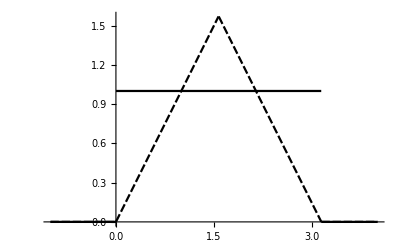

```mathematica
Plot[{f1[t],f2[t]},{t,-1,4}]
```

Теперь можем найти решение:

```mathematica
dssolve[t,{x''[t]-y'[t]==f1[t],x[t]+y'[t]==f2[t]},{x[0]->0,y[0]->0,x'[0]->0,y'[0]->0}]
```

x[t]= (1+t-Cos[t]+(π-2 t-2 Cos[t]) HeavisideTheta[-π/2+t]-Sin[t]+HeavisideTheta[-π+t] (-1-π+t-Cos[t]+Sin[t]))

y[t]= (1-t-Cos[t]+2 HeavisideTheta[-π/2+t] (-1+Sin[t])+Sin[t]+HeavisideTheta[-π+t] (1-π+t+Cos[t]+Sin[t]))

Примечание: можно было бы составить модуль для решения систем с произвольным количеством неизвестных функций, но это было бы слишком трудоемко и выходило бы за рамки данного курса, поэтому модуля для произвольного количества писать не будем.

### 3.3.2. Решение линейных интегральных и интегро-дифференциальных уравнений.

Используя теорему свертывания, можно легко найти изображения решений интегральных уравнений Вольтерра 1-ого и 2-ого рода в том случае, когда ядром в соответствующем уравнении служит функция вида K(t-τ), где K(t) - оригинал. Этот метод применим и к интегро-дифференциальных уравнениям с таким же ядром.

##### Пример №13.139

Решить следующее интегральное уравнение:

∫_0^t ch(t-τ)x(τ)ⅆτ=ch t - cos t

Метод решения подобных уравнений ничем не отличается от рассмотренного ранее метода решения дифференциальных уравнений.

Напомним, что по теореме свертывания:

∫_0^t f(t-τ)x(τ)ⅆτ=(f*x )(t)≐F(p)·X(p)

Найдем изображение исходного уравнения:

```mathematica
LaplaceTransform[Integrate[Cosh[t-τ]x[τ],{τ,0,t}]==Cosh[ t] - Cos [t],t,p]
```

(p LaplaceTransform[x[t],t,p])/(-1+p^2)==p/(-1+p^2)-p/(1+p^2)

Таким же образом, как и раньше, обозначим LaplaceTransform[x[t],t,p] как X[p].

```mathematica
dif=LaplaceTransform[Integrate[Cosh[t-τ]x[τ],{τ,0,t}]==Cosh[ t] - Cos [t],t,p]/.LaplaceTransform[x[t],t,p]->X[p]
```

(p X[p])/(-1+p^2)==p/(-1+p^2)-p/(1+p^2)

Теперь из этого уравнения необходимо выразить функцию X(p):

```mathematica
Solve[dif,X[p]]
```

{{X[p]→2/(1+p^2)}}

Теперь, зная выражения для изображения, найдем функцию-решение исходного дифференциального уравнения:

```mathematica
InverseLaplaceTransform[2/(1+p^2),p,t]
```

2 Sin[t]

Итак, ответ:

x(t)=2sin t

Если посмотреть внимательно, то можно убедиться, что последовательность действий, примененная для решения интегрального уравнения, полностью совпадает с последовательностью решения дифференциальных уравнений, следовательно, мы можем воспользоваться, написанным нами ранее модулем dsolve, с пустыми начальными условиями. Убедимся в этом:

```mathematica
dsolve[t,Integrate[Cosh[t-τ]x[τ],{τ,0,t}]==Cosh[ t] - Cos [t],{}]
```

2 Sin[t]

Получили, как и ожидалось, тот же самый ответ. Следовательно, данный модуль можно, в каком-то роде, назвать универсальным.

##### Пример №13.141

Решить интегро-дифференциальное уравнение:

∫_0^t ⅇ^(t-τ)sin(t-τ)x(τ)ⅆτ=x''-x'+ⅇ^t(1-cos t), x(0)=x'(0)=1

Данной уравнение содержит и интеграл и дифференциал неизвестной функции, поэтому и называется интегро-дифференциальным уравнением.

Однако, способ решения и такого уравнения, ничем не отличается от рассмотренного ранее.

Следовательно, воспользуемся модулем dsolve:

```mathematica
dsolve[t,Integrate[Exp[t-τ]Sin[t-τ]x[τ],{τ,0,t}]==x''[t]-x'[t]+Exp[t](1-Cos[t]),{x[0]->1,x'[0]->1}]
```

ⅇ^t

Убедимся, что ответ получен верно, подставив полученную функцию в исходное уравнение:

```mathematica
Integrate[Exp[t-τ]Sin[t-τ]x[τ],{τ,0,t}]==x''[t]-x'[t]+Exp[t](1-Cos[t])/.x[s_]->Exp[s]
```

-ⅇ^t (-1+Cos[t])==ⅇ^t (1-Cos[t])-x'[t]+x''[t]

К сожалению функция ReplaceAll (/.) не заменяет x’(t) на e^t’, поэтому немного перепишем исходное уравнение:

```mathematica
Integrate[Exp[t-τ]Sin[t-τ]x[τ],{τ,0,t}]==D[x[t],{x,2}]-D[x[t],x]+Exp[t](1-Cos[t])/.x[s_]->Exp[s]
```

-ⅇ^t (-1+Cos[t])==ⅇ^t (1-Cos[t])

Функция удовлетворяет уравнению, следовательно решение верно.

Ответ:

x(t)=ⅇ^t

##### Пример №13.143

Проинтегрировать уравнение Абеля:

∫_0^t (x(τ))/(√(t-τ))ⅆτ==π

Разумеется и данное уравнение входит в класс задач, который в силах разрешить функция dsolve. Воспользуемся ей, для решения данного уравнения:

```mathematica
dsolve[t,Integrate[x[τ](t-τ)^(-1/2),{τ,0,t}]==Pi,{}]
```

1/(√t)

Получили, что решением уравнения Абеля является функция:

x(t)=1/(√t)

Выполним проверку, подставим функцию в исходное уравнение:

```mathematica
Integrate[x[τ](t-τ)^(-1/2),{τ,0,t}]==Pi/.x[t_]->1/√t
```

ConditionalExpression[True,Re[t]>0&&Im[t]==0]

Получили верное равенство, при условии, что действительная часть t больше нуля, мнимая часть равна нулю.

Следует сказать, что данное уравнение, является частным случаем следующего уравнения:

##### Пример №13.144

Проинтегрировать уравнение Абеля:

∫_0^t (x(τ))/(t-τ)^α ⅆτ==t^β, 0≤ α<1,  β>-1

Решим его, с помощью функции dsolve:

```mathematica
dsolve[t,Integrate[x[τ](t-τ)^-α,{τ,0,t}]==t^β,{}]
```

(t^(-1+α+β) Gamma[1+β])/(Gamma[1-α] Gamma[α+β])

Решение запишем в традиционной форме:

x(t)=(Г(1+β))/(Г(1-α))t^(-1+α+β)/(Г(α+β))

где Г(t) - гамма-функция.

Убедимся в правильности решения:

```mathematica
Integrate[x[τ](t-τ)^-α,{τ,0,t}]==t^β/.x[t_]-> (t^(-1+α+β) Gamma[1+β])/(Gamma[1-α] Gamma[α+β])
```

ConditionalExpression[True,Re[α]<1&&Re[α+β]>0&&Re[t]>0&&Im[t]==0]

Верно, при α<1, a+β>0 или β>-1, что полностью совпадает с условиями задачи.

### 3.3.3. Вычисление несобственных интегралов.

Один из способов вычисления несобственных интегралов вида ∫_0^∞ f(t)ⅆt основан на примеении теоремы операционного исчисления о связи “конечного” значения оригинала и “начального” значения изображения. Докажем эту теорему:

Теорема:

Если f(t)≐F(p) и существует конечный предел lim_(t→+∞) f(t)=f(+∞), то

f(+∞)=lim_(p→0) p F(p)

Доказательство:

Воспользуемся теоремой подобия:

f(a t)≐1/a F(p/a)

Значению f(+∞) соответстует:

lim_(a→∞) f(a t)=f(+∞)

Тогда, согласно теореме подобия, получим:

lim_(a→+∞) f(a t)=f(+∞)=lim_(a→+∞) 1/a F(p/a)

введем обозначение :p=p/a, тогда:

lim_(a→+∞) 1/a F(p/a)=lim_(p→+0) p F(p)

Отсюда:

f(+∞)=lim_(p→+0) p F(p)

Из этой теоремы и соотношения:

∫_0^t f(t)ⅆt=1/p F(p)

при условии сходимости интеграла следует соотношение:

∫_0^(+∞) f(t)ⅆt=F(0)

##### Пример №13.149

Вычислить несобественный интеграл:

∫_0^(+∞) t^μ ⅇ^(-α t)ln tⅆt, α,μ>-1

Сначала, попробуем напрямую посчитать значения данного интеграла с помощью функции Integrate:

```mathematica
Integrate[t^μ Exp[-α t]Log[t],{t,0,Infinity},Assumptions->α>0&&μ>-1]
```

-α^(-1-μ) μ Gamma[μ] (EulerGamma-HarmonicNumber[μ]+Log[α])

Возможно ответ был бы получен, но после десятиминутного ожидания, результатов не было. Из этого можно сделать вывод, что использование вспомогательного метода, описанного выше, вполне рационально и даже необходимо.

Найдем изображение подинтегральной функции с помощью LaplaceTransform:

```mathematica
i=LaplaceTransform[t^μ Exp[-α t]Log[t],t,p]
```

-(p+α)^(-1-μ) μ Gamma[μ] (EulerGamma-HarmonicNumber[μ]+Log[p+α])

EulerGamma- постоянная Эйлера, численно равная γ≃0.577216, HarmonicNumber[μ] функия гармонического числа, которая задается:

HarmonicNumber[μ]=H_μ=∑_(i=1)^μ 1/i

Итак, мы получили изображение подинтегральной функции, теперь, чтобы получить значение несобственного интеграла, просто подставим p=0

```mathematica
i/.p->0
```

-α^(-1-μ) μ Gamma[μ] (EulerGamma-HarmonicNumber[μ]+Log[α])

Данный ответ сходится, с тем, что бы мы получили воспользовавшись функцией Integrate:

```mathematica
Integrate[t^μ Exp[-α t]Log[t],{t,0,Infinity},Assumptions->μ>-1&&α>0]
```

-α^(-1-μ) μ Gamma[μ] (EulerGamma-HarmonicNumber[μ]+Log[α])

Однако, следует сказать, что время ее работы, значительно превосходит время, затраченное на вычисление значения интеграла, способом выше.

Пусть функции

f(t,u) и ψ(t,u)=∫_0^(+∞) ϕ(u)f(t,u)ⅆu

являются оригиналами. Тогда, применяя теорему об интегрировании по параметру, будем иметь:

ψ(t)≐Ψ(p)=∫_0^(+∞) ϕ(u)F(p,u)ⅆu

Поэтому, если интеграл определяющий Ψ(p), можно вычислить, то для отыскания интеграла ψ(t) достаточно найти оригинал для Ψ(p),т.е.

∫_0^(+∞) ϕ(u)f(t,u)ⅆu≐∫_0^(+∞) ϕ(u)F(p,u)ⅆu

Пример №13.152

Вычислить несобственный интеграл:

∫_0^(+∞) ⅇ^(-t u^2)ⅆu

В данной задаче имеем:

ϕ(u)=1, f(t,u)=ⅇ^(-t u^2)

Тогда, чтобы вычислить значение интерграла, найдем изображение функци f:

```mathematica
LaplaceTransform[Exp[-t u^2],t,p]
```

1/(p+u^2)

Теперь найдем значение следующего интеграла:

Ψ(p)=∫_0^(+∞) 1/(p+u^2)ⅆu

Найдем его значение с помощью функции Integrate:

```mathematica
Integrate[1/(p+u^2),{u,0,Infinity}]
```

ConditionalExpression[π/(2 √p),Im[p]≠0||Re[p]≥0]

Теперь просто находим оригинал получившейся функции Ψ:

```mathematica
InverseLaplaceTransform[π/(2 √p),p,t]
```

(√π)/(2 √t)

Получили, что:

∫_0^(+∞) ⅇ^(-t u^2)ⅆu=(√π)/(2 √t)

Проверим ответ, напрямую найдя интеграл:

```mathematica
Integrate[Exp[-t u^2],{u,0,Infinity}]
```

ConditionalExpression[(√π)/(2 √t),Re[t]>0]

Ответ получился тем же самым, следовательно решение получено верно.

Т е о р е м а  П а р с е в а л я. Если

f_1(t)≐F_1(p), f_2(t)≐F_2(p) и F_1(p),F_2(p) аналитичны при Re p≥ 0, то

∫_0^∞ f_1(u)F_2(u)ⅆu=∫_0^∞ F_1(v)f_2(v)ⅆv

##### Пример №13.153

Вычислить несобственный интеграл, используя теорему Парсеваля:

∫_0^(+∞) (ⅇ^(-α u)-ⅇ^(-β u))/(√u)ⅆu

Введем следующие обозначения:

f_1(u)=ⅇ^(-α u)-ⅇ^(-β u), F_2(u)=1/(√u)

Тогда, согласно теореме Парсеваля (5), для того чтобы вычислить значение исходного интеграла, необходимо найти изображение функции f_1, и оригинал функции F_2, сделаем это, при помощи функций LaplaceTransform, и InverseLaplaceTransform:

```mathematica
LaplaceTransform[Exp[-α u]-Exp[-β u],u,v]
```

1/(v+α)-1/(v+β)

F_1(v)=1/(v+α)-1/(v+β)

```mathematica
InverseLaplaceTransform[1/(√u),u,v]
```

1/(√π √v)

f_2(v)=1/(√π √v)

Теперь, найдем значение исходного интеграла по формуле (5):

```mathematica
Integrate[1/(√π √v)(1/(v+α)-1/(v+β)),{v,0,Infinity},Assumptions->α>0&&β>0]
```

√π (1/(√α)-1/(√β))

Получили ответ:

∫_0^(+∞) (ⅇ^(-α u)-ⅇ^(-β u))/(√u)ⅆu=1/(√π)∫_0^(+∞) 1/(√v)(1/(v+α)-1/(v+β))ⅆu=√π (1/(√α)-1/(√β))

### 3.3.4. Суммирование рядов.

Методы операционного исчисления могут быт ьиспользованы при суммировании числовых и функциональных рядов.

Пусть F(p) является изображением для f(t) (область аналитичности F(p): Re p⩾k),  тогда сумма ряда S

S=∑_(n=k)^∞ (±1)^n F(n)

можт быть найдена по формуле:

S=(±1)^k∫_0^∞ (ⅇ^(-k t)f(t))/(1∓ⅇ^-t)ⅆt

Докажем это:

F(p)=∫_0^∞ ⅇ^(-p t)f(t)ⅆt (по определению преобразования Лапласа)
Имеем: ((±1)^k ⅇ^(-k t))/(1∓ⅇ^-t)=∑_(n=k)^∞ (±1)^n ⅇ^(-n t)

```mathematica
Sum[(-1)^n Exp[- n t],{n,k,Infinity}]
```

((-1)^k ⅇ^(t-k t))/(1+ⅇ^t)

Поэтому:

(±1)^k∫_0^(+∞) (ⅇ^(- k t)f(t))/(1∓ⅇ^-t)ⅆt=∫_0^(+∞) f(t)∑_(n=k)^∞ (±1)^n ⅇ^(-n t)ⅆt=
=∑_(n=k)^∞ (±1)^n∫_0^(+∞) f(t)ⅇ^(-n t)ⅆt=∑_(n=k)^∞ (±1)^n F(n)

##### Пример №13.156

Используя формулу (6), найти сумму числового ряда:

∑_(n=1)^∞ n/((n^2-1/4)^2)

Данный имеет следующую структуру:

∑_(n=1)^∞ (+1)^n F(n), где F(n)=n/((n^2-1/4)^2)

Тогда, для того чтобы вычислить сумму данного числового ряда, необходимо найти оригинал функции F(n), сделаем это, обратившись к  функции InverseLaplaceTransofrm:

```mathematica
InverseLaplaceTransform[n/((n^2-1/4)^2),n,t]
```

1/2 ⅇ^(-t/2) (-1+ⅇ^t) t

Итак получили, что:

f(t)=1/2 ⅇ^(-t/2) (-1+ⅇ^t) t

Теперь вычислим сумму ряда по формуле (6):

∑_(n=1)^∞ n/((n^2-1/4)^2)=(+1)^1∫_0^(+∞) f(t) ⅇ^(-1 t)/(1-ⅇ^-t)ⅆt

```mathematica
Integrate[1/2 ⅇ^(-t/2) (-1+ⅇ^t) t  Exp[-t]/(1-Exp[-t]),{t,0,Infinity}]
```

2

Сумма исходного ряда равна:

∑_(n=1)^∞ n/((n^2-1/4)^2)=2

Убедимся в этом, посчитая сумму ряда напрямую:

```mathematica
Sum[n/((n^2-1/4)^2),{n,1,Infinity}]
```

2

Получили тот же самый ответ.

Пусть f(t) является оригиналом функции F(P) (область аналитичности F(p): Re p⩾0). Пусть, кроме того, Φ(t,x) - производящая функция бесконечной последовательности функции:

Φ(t,x)=∑_(n=0)^∞ ϕ_n(x)t^n

Сумма S(x) сходящегося на [a,b] функционального ряда

∑_(n=0)^∞ F(n)ϕ_n(x)

может быть найдена по формуле:

S(x)=∫_0^(+∞) f(t)Φ(ⅇ^-t,x)ⅆt

Докажем это:

∫_0^(+∞) f(t)Φ(ⅇ^-t,x)ⅆt=∫_0^(+∞) f(t)∑_(n=0)^∞ ϕ_n(x)ⅇ^(-n t)ⅆt=
=∑_(n=0)^∞ ϕ_n(x)∫_0^(+∞) f(t)ⅇ^(-n t)ⅆt=∑_(n=0)^∞ ϕ_n(x)F(n)=S(x)

##### Пример №13.160

Используя формулу (7), с помощью подходящей производящей функции просуммировать следующий ряд:

∑_(n=0)^∞ (-1)^n x^(2n+1)/(2n+1)

Главная задача, при использовании формулы (7) выбрать наиболее удобную производящую функцию. Пусть Ф(t,x):

Φ(t,x)=∑_(n=0)^∞ (-1)^n x^(2n+1)t^n=x∑_(n=0)^∞ (-1)^n x^(2n)t^n=x∑_(n=0)^∞ (-1)^n(x^2 t)^n
∑_(n=0)^∞ (-1)^n(x^2 t)^n=1/(1+x^2 t) - сумма геометрической прогрессии.

В итоге:

Φ(t,x)=x/(1+x^2 t)

Запишем функцию Φ от t и x:

```mathematica
Φ[t_,x_]:=x/(1+x^2 t)
```

Теперь найдем оригинал функции F(n), которая в нашем случае равна:

F(n)=1/(2n+1)

Воспользуемся InverseLaplaceTransform:

```mathematica
InverseLaplaceTransform[1/(2n+1),n,t]
```

ⅇ^(-t/2)/2

Получили, что оригинал функции F(p):

f(t)=ⅇ^(-t/2)/2

Осталось лишь по формуле (7) вычислить интеграл:

```mathematica
Integrate[ⅇ^(-t/2)/2 Φ[Exp[-t],x],{t,0,Infinity},Assumptions->-1<x<1]
```

ArcTan[x]

Итак получили, что сумма исходного ряда равна:

∑_(n=0)^∞ (-1)^n x^(2n+1)/(2n+1)=arctan x

Воспользуемся функцией Sum, чтобы убедится в этом:

```mathematica
Sum[(-1)^n x^(2n+1)/(2n+1),{n,0,Infinity}]
```

ArcTan[x]

Что подтверждает верность полученного нами ответа.

## 3.4. Дискретное преобразование Лапласа и его применение

### 3.4.1. Z-преобразование и дискретное преобразование Лапласа.

Z-преобразованием числовой (действительной или комплексной) бесконечной последовательности (a_n) называется функция комплексной переменной F(z), определяемая при |z| >R=lim_(n→∞) (|a_n|)^(1/n) рядом Лорана

F(z)=∑_(n=0)^∞ a_n/z^n

и аналитически продолженная в круг |z|<R. Если последовательность удовлетворяет условию |a_n|<M ⅇ^(α n) (M>0, α - постояне), то функция F(z) будет аналитической в области |z| >ⅇ^α, т.е. вне круга с центром в нулевой точке и радиусом R=ⅇ^α.

Формула (1) дает разложение F(z)  в ряд Лорана в окрестности бесконечно удаленной точки (являющейся правильной точкой F(z)), поэтому для восстановления последовательности (a_n) по ее Z-преобразованию надо F(z) любым способом разложить в ряд Лорана в окрестности бесконечно удаленной точки; в частности, можно воспользоваться формулой для определения коэффициентов этого разложения:

a_n=1/(2π ⅈ)∫_C F(z)z^(n-1)ⅆz

( C - контур, внутри которго лежат все особые точки функции F(z))

Введем решетчатую функцию f(n), полагая что a_n=f(n). По-прежнему f(n) удовлетворяет условию |f(n)|<M ⅇ^(α n), и примем дополнительно, что f(n)=0, при n<0; такие решетчатые функции будем называть дискретным оригиналом.
Дискретное преобразование Лапласа функции f(n) мы получим, если в Z-преобразовании положим z=ⅇ^q:

F(q)=∑_(n=0)^∞ f(n)ⅇ^(-n q)

Связь между дискретным оригиналом и его изображением будем обозначать:

f(n)≐F(q), либо  𝒟[f]=F(q)

Изображение F(q) - функция комплексной переменной с периодом 2 π, при этом в основной полосе -π<Im q< π она алитична только 
при Re q > α. Таким образомвсе ее особые точки лежат в этой полосе слева от прямой Re q = α.

Из формулы (3) вытекает следующая формула обращения дискретного преобразования Лапласа:

f(n)=1/(2π ⅈ)∫_(γ-π ⅈ)^(γ+π ⅈ) F(q)ⅇ^(n q)ⅆq

### Свойства дискретного преобразования Лапласа

1. Л и н е й н о с т ь.

∑_(j=0)^∞ C_j f_j(n)≐∑_(j=0)^∞ C_j F_j(q)

2. Ф о р м у л а  с м е щ е н и я.

e^(α n)f(n)≐F(q-a)

3. Ф о р м у л ы  з а п а з д ы в а н и я  и  о п е р е ж е н и я.

f(n-k)≐e^(-k q)F(q)
f(n+k)≐e^(k q)(F(q)-∑_(r=0)^(k-1) f(r)e^(-r q))

4. Д и ф ф е р е н ц и р о в а н и е  п о  п а р а м е т р у.

Если f(n,x)≐F(q,x), то ∂/(∂x)f(n,x)≐∂/(∂x)F(q,x)

5. Д и ф ф е р е н ц и р о в а н и е  и  и н т е г р и р о в а н и е  и з о б р а ж е н и я.

n^k f(n)≐(-1)^k ⅆ^k/(ⅆ q^k)F(q)
(f(n))/n≐∫_q^∞ (F(s)-f(0))ⅆs

6. И з о б р а ж е н и е  к о н е ч н ы х  р а з н о с т е й  о р и г и н а л а.

Δ^k f(n)≐(e^q-1)^k F(q)-e^q∑_(r=0)^(k-1) (e^q-1)^(k-r-1)Δ^r f(0)

7. И з о б р а ж е н и е  к о н е ч  н ы х  с у м м  о р и г и н а л а.

Если, g(n)=∑_(k=0)^(n-1) f(k), то g(n)≐(F(q))/(e^q-1)

8. У м н о ж е н и е  и з о б р а ж е н и й

Если f_1(n)*f_2(n)=∑_(r=0)^n f_1(r)f_2(n-r), то f_1(n)*f_2(n)≐F_1(q)·F_2(q)

Приведем список изображений основных решетчатых функций:

f(n)=Piecewise[{{C, n=0}, {0, n≠ 0}}],                                                             F(q)=C
η(n)=Piecewise[{{1, n≥ 0}, {0, n< 0}}] ,                                                     F(q)=e^q/(e^q-1)
f(n)=a^n,                                                                       F(q)=e^q/(e^q-a)
f(n)=e^(α  n),                                                                    F(q)=e^q/(e^q-e^α)
f(n)=n,                                                                       F(q)=e^q/((e^q-1)^2)
f(n)=n^2,                                                                     F(q)=(e^q(e^q+1))/((e^q-1)^3)
f(n)=n^[2]/(2!)=(n(n-1))/2=C_n^2,                                  F(q)=e^q/((e^q-1)^3)
f(n)=n^[k]/(k!)=(n(n-1)...(n-k+1))/(k!)=C_n^k,       F(q)=e^q/((e^q-1)^(k+1))
f(n)= sin β n,                                           F(q)=  (e^q sin β)/(e^(2q)+1-2 e^q cos β)
f(n)=cos β n,                                            F(q)=  (e^q(e^q-cos β))/(e^(2q)+1-2 e^q cos β)
f(n)=sh β n,                                                   F(q)= (e^q sh β)/(e^(2q)+1-2 e^q ch β)
f(n)=ch β n,                                                     F(q)= (e^q(e^q-ch β))/(e^(2q)+1-2 e^q ch β)
f(n)=n^[k]/(k!)e^(α n)=C_n^k e^(α n),                                            F(q)=e^(q+k α)/((e^q-e^α)^(k+1))
f(n)=n^[k]/(k!)a=C_n^k a^n,                                                       F(q)=(a^k e^q)/((e^q-a)^(k+1))

##### Пример №13.174

Найти изображение следующей функции:

f(n)=ⅇ^(a n)cos β n

Воспользовавшись формулой смещения

e^(a n)f(n)≐F(q-a)

Получим, что изображение заданной функции:

F(q)=(e^(q-a)(e^(q-a)-cos β))/(e^(2q-2a)+1-2 e^(q-a)cos β)

##### Пример №13.177

Найти изображение следующей функции:

f(n)=n^2 a^n

Согласно свойству 5 (дифференцирование изображения), имеем формулу:

n^2 f_1(n)≐ⅆ^2/(ⅆ q^2)F_1(q)
f_1(n)≐F_1(q), f_1(n)=a^n

Найдем вторую проивзодную от функции F_1(q):

```mathematica
D[Exp[q]/(Exp[q]-a),{q,2}]//Simplify
```

(a ⅇ^q (a+ⅇ^q))/((-a+ⅇ^q)^3)

Получаем, что:

f(n)=n^2 a^n≐(a ⅇ^q (a+ⅇ^q))/((-a+ⅇ^q)^3)

Разумеется каждый раз искать и комбинировать необходимые свойства слишком утомительно, да и не нужно. Воспользуемся встроенной в систему функцией ZTransform, которая, как очевидно из названия, совершает Z-преобразование заданной дискретной функции.

```mathematica
ZTransform[n^2 a^n,n,z]
```

(a z (a+z))/(-a+z)^3

Теперь произведем замену:

```mathematica
ZTransform[n^2 a^n,n,z]/.z->Exp[q]
```

(a ⅇ^q (a+ⅇ^q))/((-a+ⅇ^q)^3)

Получили тот же самый ответ. Функция ZTransform, как видно из примера, имеет ту же структуру, что и функции InverseLaplaceTransform и LaplaceTransform.

Рассмотрим еще несколько примеров:

##### Пример №13.180

Найти изображение следующей функции:

f(n)=(sin β n)/n

```mathematica
ZTransform[Sin[β n]/n,n,z]/.z->Exp[q]
```

β+ArcTan[Sin[β]/(ⅇ^q-Cos[β])]

Вместо замены z на e^q, можно сразу, в аргументах функции ZTransform указывать не z, а e^q:

```mathematica
ZTransform[Sin[β n]/n,n,Exp[q]]
```

β+ArcTan[Sin[β]/(ⅇ^q-Cos[β])]

Получили

(sin β n)/n≐β+arctan(sin(β))/(ⅇ^q-cos(β))

##### Пример №13.181

Найти решетчатую функцию по её изображенияю

F(q)=e^q/((e^q-1)(e^(2q)-4))

Для того чтобы найти решетчатую функцию разложим изображение на простые дроби:

```mathematica
Apart[1/((Exp[q]-1)(Exp[2q]-4))]
```

1/(4 (-2+ⅇ^q))-1/(3 (-1+ⅇ^q))+1/(12 (2+ⅇ^q))

И домножим на экспоненту:

```mathematica
Expand[Apart[1/((Exp[q]-1)(Exp[2q]-4))]Exp[q]]
```

ⅇ^q/(4 (-2+ⅇ^q))-ⅇ^q/(3 (-1+ⅇ^q))+ⅇ^q/(12 (2+ⅇ^q))

Получили 3 простые дроби. По свойству линейности находим оригинал каждой дроби отдельно:

ⅇ^q/(4 (-2+ⅇ^q))≐1/4 2^n=(2^n)^-2
-ⅇ^q/(3 (-1+ⅇ^q))=-1/3 1^n=-1/3
ⅇ^q/(12 (-(-2)+ⅇ^q))=1/12(-2)^n=1/3 (-1)^n 2^(-2+n)

Таким образом получили:

ⅇ^q/(4 (-2+ⅇ^q))-ⅇ^q/(3 (-1+ⅇ^q))+ⅇ^q/(12 (2+ⅇ^q))≐2^(-2+n)-1/3+1/3 (-1)^n 2^(-2+n)

Решим задачу вторым способом.

С помощью замены e^q на z и используя формулу обращения (2), сведем задачу поиска ориганала к вычислению контурного интеграла:

e^q/((e^q-1)(e^(2q)-4))→ z/((z-1)(z^2-4))
a_n=1/(2π ⅈ)∫_C (z z^(n-1))/((z-1)(z^2-4))ⅆz

Для этого обратимся integrateR из главы 2 раздела 6 Вычеты и их применение:

```mathematica
integrateR[z,1/(2 Pi I)z^n/((z-1)(z^2-4)),0,4]//Simplify//Expand
```

-1/3+2^(-2+n)+1/3 (-1)^n 2^(-2+n)

Получили тот же самый ответ.

##### Пример №13.182

Найти решетчатую функцию по её изображенияю

F(q)=e^q/(e^(4q)+1)

Воспользуемся встроенной функцией InverseZTransform, предварительно заменив e^q на z.

```mathematica
InverseZTransform[z/(z^4+1),z,n]//FullSimplify//TrigFactor//Simplify
```

Cos[1/4 (1+n) π] Sin[(n π)/2]

С помощью небольших манипуляций приходим к удовлетворяющей нас форме ответа.

Итак, получили, что:

e^q/(e^(4q)+1)≐sin((π n)/2) cos(1/4 π (n+1))

##### Программный модуль

Так как в системе Mathematica отсутствует функция обратного дискретного преобразования, напишем такую сами:

```mathematica
inverseDTransform[expr_,q_,n_]:=Module[{},
InverseZTransform[expr/.Exp[p_]-> z^(p/q),z,n]]
```

##### Пример №13.183

Найти решетчатую функцию по её изображенияю

F(q)=e^(2q)/(e^(2q)+2 e^q+2)

Решим задачу с помощью функции inverseDTransform:

```mathematica
inverseDTransform[Exp[2q]/(Exp[2q]+2Exp[q]+2),q,n]//ExpToTrig//TrigFactor//FullSimplify
```

2^(n/2) (Cos[(3 n π)/4]-Sin[(3 n π)/4])

Получили ответ:

f(n)=2^(n/2) (cos((3 π n)/4)-sin((3 π n)/4))≐F(q)=e^(2q)/(e^(2q)+2 e^q+2)

### 3.4.2. Решение разностных уравнений.

Пусть дано уравнение

a_0 x(n+k)+a_1(n+k-1)+...+a_k x(n)=ϕ(n)

(a_0,a_1,...,a_k-постоянные) с заданными (или произвольными) начальными условиями. Правая часть уравнения (13) - решетчатая функция ϕ(n) - предполагается оригиналом.

Полагая x(n)≐X(q) и применяя формулу опережения (свойство 3, б), состовляем операторное уравнение и определяем из него X(q). Затем одним из способов по изображению найдем искомое решение x(n).

Если исходное уравнение было задано не через последователньые значения неизвестной функции, а через ее конечные разности, т.е. имеет вид

b_0 Δ^k x(n)+b_1 Δ^(k-1)x(n)+...+b_k x(n)=ϕ(n)

то вследствие громоздкости формул для отыскания изображений конечных разностей решетчатых функций (свойство 6) его следует предварительно преобразовать к виду (13) при помощи известных формул, связывающих конечные разности функции с ее последовательными значениями:

Δ^r x(n)=x(n+r)-C_r^1 x(n+r-1)+C_r^2 x(n+r-2)+...+(-1)^r x(n)

Аналогично решаются и системы разностных уравнений

##### Пример №13.189

Решить линейное разностное уравнение:

x_(n+2)-3 x_(n+1)-10 x_n=0, x_0=3,x_1=-1

Обозначим x_n≐X(q), с помощью формулы опережения, найдем следующие изображения:

x_(n+1)≐ⅇ^q(X(q)-x_0)=ⅇ^q X(q)-3 ⅇ^q
x_(n+2)≐ⅇ^(2q)(X(q)-x_0-x_1 ⅇ^-q)=ⅇ^(2q)X(q)-3 ⅇ^(2q)+ⅇ^q

Запишем эти выражения в исходное уравнение, и найдем выражение для изображения исходной функции:

ⅇ^(2q)X(q)-3 ⅇ^(2q)+ⅇ^q-3 ⅇ^q X(q)+9 ⅇ^(2q)-10X(q)=0
X(q)=(ⅇ^q (-10+3 ⅇ^q))/(-10-3 ⅇ^q+ⅇ^(2 q))

Теперь найдем оригинал с помощью функции inverseDTransform:

```mathematica
inverseDTransform[(ⅇ^q (-10+3 ⅇ^q))/(-10-3 ⅇ^q+ⅇ^(2 q)),q,n]//FullSimplify
```

1/7 ((-1)^n 2^(4+n)+5^(1+n))

Итак получили, что решение исходного уравнения функция x_n:

x_n=1/7 ((-1)^n 2^(4+n)+5^(1+n))

##### Пример №13.190

Решить линейное разностное уравнение:

x_(n+2)+x_(n+1)+x_n=0, x_0=1,x_1=-1

В этот раз найдем изображение всего уравнения:

```mathematica
ZTransform[x[n+2]+x[n+1]+x[n]==0,n,Exp[q]]
```

-ⅇ^q x[0]-ⅇ^(2 q) x[0]-ⅇ^q x[1]+ZTransform[x[n],n,ⅇ^q]+ⅇ^q ZTransform[x[n],n,ⅇ^q]+ⅇ^(2 q) ZTransform[x[n],n,ⅇ^q]==0

Заменим ZTransform[ x[n], n, Exp[q]] на функцию X[q]:

```mathematica
ZTransform[x[n+2]+x[n+1]+x[n]==0,n,Exp[q]]/.ZTransform[x[n],n,Exp[q]]-> X[q]
```

-ⅇ^q x[0]-ⅇ^(2 q) x[0]-ⅇ^q x[1]+X[q]+ⅇ^q X[q]+ⅇ^(2 q) X[q]==0

Также теперь можно учесть начальные условия:

```mathematica
ZTransform[x[n+2]+x[n+1]+x[n]==0,n,Exp[q]]/.{ZTransform[x[n],n,Exp[q]]-> X[q],x[0]->1,x[1]->-1}
```

-ⅇ^(2 q)+X[q]+ⅇ^q X[q]+ⅇ^(2 q) X[q]==0

Теперь выразим функцию X[z]:

```mathematica
Solve[-ⅇ^(2 q)+X[q]+ⅇ^q X[q]+ⅇ^(2 q) X[q]==0,X[q]]
```

{{X[q]→ⅇ^(2 q)/(1+ⅇ^q+ⅇ^(2 q))}}

Осталось лишь применить функцию inverseDTransform для того чтобы отыскать функцию x[n]:

```mathematica
inverseDTransform[ⅇ^(2 q)/(1+ⅇ^q+ⅇ^(2 q)),q,n]
```

ChebyshevU[n,-1/2]

В ответе получаем функцию многочлена Чебышева 2-ого рода, который в привычном для нас виде запишется как:

x(n)=2/(√3)sin (2π(n+1))/3

##### Пример №13.191

Решить линейное разностное уравнение:

x_(n+2)-√3 x_(n+1)+x_n=0, x_0=1/2,x_1=(√3)/2

Внимательно изучив последовательность действий, примененные в предыдущем примере, составим программный модуль для решения разностных уравнений, который имеет схожее строение с функцией dssolve из главы 3 раздела 3 (Применения операционного исчисления):

```mathematica
rSolve[n_,expr_,rules_]:=Module[{im,sol,X,z},
im=ZTransform[expr,n,z]/.rules/.ZTransform[x[n],n,z]-> X[z];
sol=Flatten@Solve[im,X[z]];
InverseZTransform[X[z]/.sol,z,n]]
```

Теперь применим его:

```mathematica
rSolve[n,x[n+2]-√3 x[n+1]+x[n]==0,{x[0]->1/2,x[1]->√3/2}]
```

1/2 ChebyshevU[n,(√3)/2]

```mathematica
RSolve[{x[n+2]-√3 x[n+1]+x[n]==0,x[0]==1/2,x[1]==√3/2},x[n],n]//FullSimplify
```

{{x[n]→1/2 (Cos[(n π)/6]+√3 Sin[(n π)/6])}}

Опять же получили многчлен Чебышева 2-ого рода, и в привычном виде он запишется как:

x(n)=sin (π(n+1))/6

##### Пример №13.195

Решить систему линейных разностныз уравнений:

Piecewise[{{x_(n+1)-x_n+y_n=3^n, }, {y_(n+1)+2 x_n=-3^n, }}]x_0=3,y_0=0

Так как принципиальная последовательность действий не изменилась, составим программный модуль для решения систем линейных рекурентных уравнений

```mathematica
rsSolve[n_,expr_,rules_]:=Module[{zam,im,sol},
zam={ZTransform[x[n],n,z]->X[z],ZTransform[y[n],n,z]->Y[z]};
im=ZTransform[expr,n,z]/.zam/.rules;
sol=Flatten@Solve[im,{X[z],Y[z]}];
Print["x[n]=",  Simplify@InverseZTransform[X[z]/.sol,z,n]];
Print["y[n]=",  Simplify@InverseZTransform[Y[z]/.sol,z,n]];]
```

```mathematica
rsSolve[n,{x[n+1]-x[n]+y[n]==3^n,y[n+1]+2x[n]==-3^n},{x[0]-> 3,y[0]->0}]
```

x[n]=(-1)^n+2^n+3^n

y[n]=2 (-1)^n-2^n-3^n